```mathematica
Clear["Global`*"]
PathNumber=2;
CodePath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Codes/0/With Lead/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Codes\\",i==3}}];
FigPath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Figures/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Figures\\",i==3}}];
SetDirectory[CodePath[PathNumber]];
Si=28;
Ox=16;
Al=27;
mH=1.7;
Fe=56;
Pb=207;
rhoPb=11.34;
rhoE=2.7;
mp=0.938;
mT[A_]:=A*mp;
q[er_,A_]:=Sqrt[2 mT[A] er];
(*Helm parameter in fm*)
c[A_]:=1.23 A^(1/3)-0.6;
a=0.52;
s=0.9;
rHelm[A_]:=Sqrt[c[A]^2+7/3 Pi^2 a^2-5 s^2];
(*hbar=0.197 GeV fm*)
F[er_,A_]:=3 Exp[(q[er,A] s/0.197)^2/2] (Sin[q[er,A] rHelm[A]/0.197]-Cos[q[er,A] rHelm[A]/0.197] q[er,A] rHelm[A]/0.197)/(q[er,A] rHelm[A]/0.197)^3;
ler[mH_,A_,randomCos_]:=(1-r[mH,A] (1-randomCos)/2);
f[A_]:=Piecewise[{{0.465,A==Ox},{0.289,A==Si},{0.089,A==Al},{0.048,A==Fe}}]/.891;
reduced[m1_,m2_]:=m1 m2/(m1+m2);
r[mH_,A_]:=4 A mp*mH/(A mp+mH)^2;
Emin=5.5*10^-7/(1-ler[mH,Si,-1]);
FE[mH_]:=Sum[f[A] (reduced[mH,mT[A]]^2 /reduced[mH,mp]/mp)^2,{A,{Si,Ox,Al,Fe}}];
FPb[mH_]:=(reduced[mH,mT[Pb]]^2 /reduced[mH,mp]/mp)^2;
SGEDsigma[x_,mH_]:=Log[0.5mH (892/300000)^2 /Emin]mH/(FE[mH]x rhoE+FPb[mH]6*2.54 rhoPb)/2/(5.62*10^23)
logspace[a_,b_,n_]:=10^Range[Log10[a],Log10[b],Log10[b/a]/(n-1)];
```

```mathematica
Export["SGED_bounds_1030100.dat",Table[{N[mH],SGEDsigma[350*30.4/10,mH],SGEDsigma[350*30.4/3.333333,mH],SGEDsigma[350*30.4,mH]},{mH,logspace[1,100,100]}]]
```

SGED_bounds_1030100.dat

```mathematica
Clear["Global`*"]
PathNumber=2;
CodePath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Codes/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Codes\\",i==3}}];
FigPath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Figures/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Figures\\",i==3}}];
SetDirectory[CodePath[PathNumber]];
v=Import["vi.dat","Data"];
vi[j_]:=If[Mod[j,10^6]==0,v[[10^6]][[1]],v[[Mod[j,10^6]]][[1]]];
Si=28;
mp=0.938;
mT[A_]:=A*mp;
reduced[m1_,m2_]:=m1 m2/(m1+m2);
r[mH_,A_]:=4 A mp*mH/(A mp+mH)^2;
Ox=16;
Al=27;
mH=1.7;
Fe=56;
rhoE=2.7;
rCos:=RandomVariate[UniformDistribution[{-1,1}]];
ler[mH_,A_,randomCos_]:=(1-r[mH,A] (1-randomCos)/2);
Emin=4*10^-8/(1-ler[mH,Si,-1]);
si0=1.11*10^-29;
f[A_]:=Piecewise[{{0.465,A==Ox},{0.289,A==Si},{0.089,A==Al},{0.048,A==Fe}}]/.891;
F=Sum[f[A] reduced[mH,mT[A]]^4/reduced[mH,mp]^2/mp^2,{A,{Si,Ox,Al,Fe}}];
s=srec={};
ni=10^8;
For[i=1,i≤ni,i++,
vc=vi[i];
en=0.5mH vc^2 Exp[-2(5.62*10^23)si0 rhoE 10^4 F/mH];
recE=10^9en r[mH,Si](1-rCos)/2;
If[en≥ Emin,s=Join[s,{{vc,en,recE}}]];
If[recE≥ 40,srec=Join[srec,{{vc,en,recE}}]];
]

Export["sSGED.dat",s];
Export["sRecSGED.dat",srec];
Export["nSGED.dat",{ni,mH,si0,Length[s],Length[srec]}];
```

```mathematica
Length[srec]
```

102

```mathematica
nSGED[[2]][[1]]
```

1.7

```mathematica
sSGED=Import["sSGED.dat","Data"];
sRecSGED=Import["sRecSGED.dat","Data"];
nSGED=Import["nSGED.dat","Data"];
c=3*10^5;
mH=nSGED[[2]][[1]];
si0=nSGED[[3]][[1]];
e=0.107;
Si=28;
N0=6.02*10^26;
mp=0.938;
mT[A_]:=A*mp;
si[si0_,A_,mH_]:=si0*(A^2 (mH+mp)/(mH+mT[A]))^2;
att=Length[sRecSGED]/Sum[nSGED[[i,1]],{i,1,Length[nSGED]}];
vAve=Sum[sRecSGED[[i,1]],{i,1,Length[sRecSGED]}]/Length[sRecSGED]
nD=(0.3/mH) att
R=2.6 10^15 e (N0/Si) nD si[si0,Si,mH] vAve
```

0.00292505

1.79992×10^-7

191200.

```mathematica
Length[sRecSGED]
```

102

```mathematica
mH
```

{{100000000},{1.7},{1.11×10^-29},{4400},{102}}⟦1,2⟧

```mathematica
Table[sRecSGED[[i,1]],{i,1,10}]
```

{0.00275737,0.00263941,0.00259764,0.00277273,0.00267973,0.00266044,0.00267128,0.00268462,0.00278428,0.00282013}

```mathematica
att
```

6684/96409

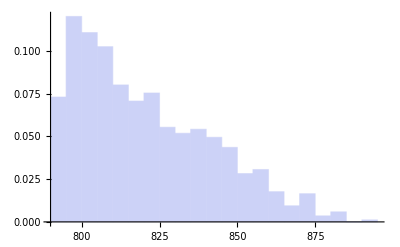

```mathematica
Histogram[Table[c sSGED[[i,1]],{i,1,Length[sSGED]}],20,"Probability"]
```